```mathematica
ClearAll["Global`*"]
```

# gsl

### Installation steps

If you want to properly embed this package into mathematica, then follow these steps:

1) run

```mathematica
SystemOpen[$UserBaseDirectory<>"/Applications"]
```

2) copy and paste gsl.wl into the Applications folder

3) To get the package in your current .nb, then run <<gsl`

#### Alternative way to install

Alternatively, the following also works so long as you have gsl.wl in the notebooks directory, such as if you downloaded this whole folder from github, you can just set the directory to the notebooks directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/alexanderpickston/Documents/GitHub/gsl

### Get package

Syntax for getting the package functionality in the notebook:

```mathematica
<<gsl`
```

gsl library has been loaded successfully. Have fun!

### Show package functions

```mathematica
?gsl`*
```

## Using function library

### A note on library usage

One thing that needs to be ironed out in this mma package is the placement of the vertecies/nodes. Applying the functions contained in this library should retain the co-ordinates of the starting graph’s vertices/nodes. The preservation of the graphs layout however is purely for the ease of use for you, the end user. If you come up with a more consistent way to do this, then please let me know (alexpickston@gmail.com).

### Reference

The figure below was taken from Hein et al_2006_Entanglement in Graph States and its Applications.

http://arxiv.org/abs/quant-ph/0602096

## Functions

### CustomGraph

```mathematica
?CustomGraph
```

A more intuitive way of creating a graph in mathematica. This methods avoids having to use symbols to define a graph. In the below example we create the “trident” graph, or graph No. 13 [ref]. For use of CustomGraph see the example below.

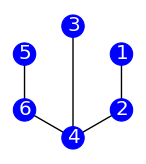

```mathematica
g=CustomGraph[{{1,2},{2,4},{4,3},{4,6},{6,5}}]
```

### LCQubit

```mathematica
?LCQubit
```

This function will apply the local complement operation to the graph you have provided it. We defined our inital graph as g, and LCQubit requires two inputs, one being the starting graph, and the vertex/node you want to apply the LC operation on. The function uses Mathematica’s built in functions.

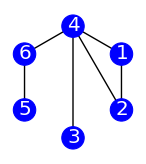

```mathematica
LC2=LCQubit[g,2]
```

### LCOrbit

```mathematica
?LCOrbit
```

This function is a bit intensive, as it applies the LCQubit function to each vertex/node. This generates a list of graphs, which the function then goes through in order to remove duplicated graphs. The outcome should be the LC orbit for said graph. This needs to be tested in more detail.

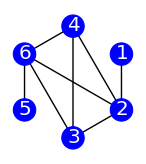
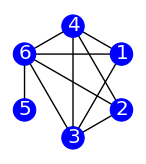
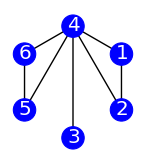
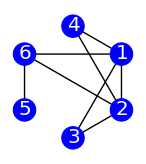
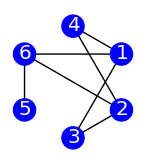
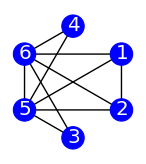
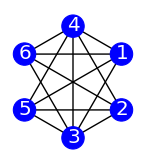
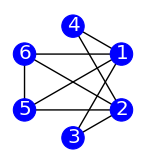
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LCOrbit[g]
```

### Zmeasurement

```mathematica
?Zmeasurement
```

Pretty self explanatory, give this function a graph and a vertex/node as inputs, and it will return the graph after a pauli Z measurement is made on said vertex/node. NOTE: Unfortunately, the co-ordinates of the vertices/nodes are not preserved when you run this function. Something I am working on.

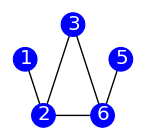

```mathematica
Zmeasurement[-Graphics-,4]
```

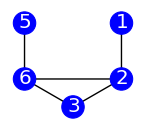
```mathematica
Zmeasurement[-Graphics-,1]
```

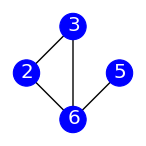

#### Another example

Starting with the trident

```mathematica
g
```

-Graphics-

From inspection, if one measures Z on node 4, then the only edges remaining are between 5 - 6, and 1 - 2.

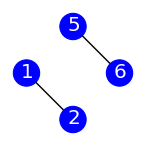

```mathematica
Zmeasurement[g,4]
```

### Ymeasurement

```mathematica
?Ymeasurement
```

A measurement in the Y basis will return the graph corresponding to a Z measurement being applied to the LC rotated graph. So the operation returns the LC rotated graph using LCQubit and then applied a Zmeasurement.

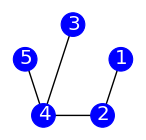

```mathematica
Ymeasurement[g,6]
```

### Xmeasurement

```mathematica
?Xmeasurement
```

These result of this measurement may be different each time it is ran.  This is because the operation includes a random choice of neighbouring vertices. More explicitly, the function randomly chooses a random neighbour of the input node. It then applies the Ymeasurement function to said neighbouring node, returning the new graph.

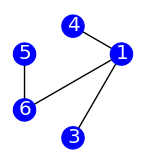

```mathematica
Xmeasurement[g,2]
```

### FindStabilizers

```mathematica
?FindStabilzers
```

Akin to the LCOrbit function, user caution is advised as the function is a brute force search. From the a set {𝕀, ℤ, 𝕏, -ℤ}, find all combinations that,when applied to a state, leaves the state vector in an eigenstate of itself with eigenvalue +1. Once it finds this it will return the makeup of the stabilizer by providing the qubit operation and the index of that operation. See example below:

```mathematica
state=(1/Sqrt[2])*(Kron[h,h,h,h]+Kron[v,v,v,v])
```

{{1/(√2)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1/(√2)}}

```mathematica
stabilizers=FindStabilzers[state];
stabilizers//TableForm
```

𝕀[1] | 𝕀[2] | 𝕀[3] | 𝕀[4]
𝕀[1] | 𝕀[2] | ℤ[3] | ℤ[4]
𝕀[1] | 𝕀[2] | -ℤ[3] | -ℤ[4]
𝕀[1] | ℤ[2] | 𝕀[3] | ℤ[4]
𝕀[1] | ℤ[2] | ℤ[3] | 𝕀[4]
𝕀[1] | -ℤ[2] | 𝕀[3] | -ℤ[4]
𝕀[1] | -ℤ[2] | -ℤ[3] | 𝕀[4]
𝕏[1] | 𝕏[2] | 𝕏[3] | 𝕏[4]
ℤ[1] | 𝕀[2] | 𝕀[3] | ℤ[4]
ℤ[1] | 𝕀[2] | ℤ[3] | 𝕀[4]
ℤ[1] | ℤ[2] | 𝕀[3] | 𝕀[4]
ℤ[1] | ℤ[2] | ℤ[3] | ℤ[4]
ℤ[1] | ℤ[2] | -ℤ[3] | -ℤ[4]
ℤ[1] | -ℤ[2] | ℤ[3] | -ℤ[4]
ℤ[1] | -ℤ[2] | -ℤ[3] | ℤ[4]
-ℤ[1] | 𝕀[2] | 𝕀[3] | -ℤ[4]
-ℤ[1] | 𝕀[2] | -ℤ[3] | 𝕀[4]
-ℤ[1] | ℤ[2] | ℤ[3] | -ℤ[4]
-ℤ[1] | ℤ[2] | -ℤ[3] | ℤ[4]
-ℤ[1] | -ℤ[2] | 𝕀[3] | 𝕀[4]
-ℤ[1] | -ℤ[2] | ℤ[3] | ℤ[4]
-ℤ[1] | -ℤ[2] | -ℤ[3] | -ℤ[4]

Lets take a few of the above and confirm

```mathematica
s0={{1,0},{0,1}};
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
```

```mathematica
{Kron[s0,s0,s0,s0].state==state,
Kron[-sz,-sz,sz,sz].state==state,
Kron[-sz,-sz,-sz,-sz].state==state}
```

{True,True,True}

### FindGraph

```mathematica
?FindGraph
```

This function will return a list of stabilizers which will define the graph a state generates.

```mathematica
FindGraph[state]//TableForm
```

𝕀[1]
𝕀[2]
𝕏[3]
ℤ[4] | 𝕀[1]
𝕏[2]
𝕀[3]
ℤ[4] | ℤ[1]
ℤ[2]
ℤ[3]
𝕏[4] | 𝕏[1]
𝕀[2]
𝕀[3]
ℤ[4]
𝕀[1]
𝕀[2]
ℤ[3]
𝕏[4] | 𝕀[1]
𝕏[2]
ℤ[3]
𝕀[4] | ℤ[1]
ℤ[2]
𝕏[3]
ℤ[4] | 𝕏[1]
𝕀[2]
ℤ[3]
𝕀[4]
𝕀[1]
ℤ[2]
𝕀[3]
𝕏[4] | 𝕀[1]
ℤ[2]
𝕏[3]
𝕀[4] | ℤ[1]
𝕏[2]
ℤ[3]
ℤ[4] | 𝕏[1]
ℤ[2]
𝕀[3]
𝕀[4]

### DrawGraph

```mathematica
?DrawGraph
```

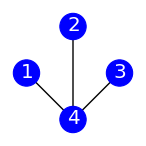
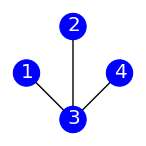
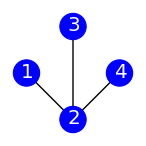

```mathematica
DrawGraph/@FindGraph[state]
```